```mathematica
SetDirectory["~/Dropbox/PMB/PMBModel"];
```

```mathematica
wsf=Transpose[Import["PMBIslands.tif","Data"]]/255;
wsf=wsf/.{0.->0};
dim=Dimensions[wsf]
RegBound=QuantityMagnitude[Import["PMBIslands.tif",{"GeoTIFF","SpatialRange"}]][[{1,2}]]

xcoord=Table[RegBound[[1,1]]+(x-1)/(dim[[1]]-1)*(RegBound[[1,2]]-RegBound[[1,1]]),{x,dim[[1]]}];
ycoord=Table[RegBound[[2,2]]-(y-1)/(dim[[2]]-1)*(RegBound[[2,2]]-RegBound[[2,1]]),{y,dim[[2]]}];
```

{433,244}

{{32.23,32.62},{-0.38,-0.16}}

```mathematica
Coo={};
Do[
If[wsf[[i,j]]>0 ,
AppendTo[Coo,{xcoord[[i]],ycoord[[j]],N[wsf[[i,j]]],1}]],{i,dim[[1]]},{j,dim[[2]]}];
```

```mathematica
relsite={{32.61,-0.32},{32.33,-.198}};
contsite={{32.57,-0.333},{32.3,-0.19}};
reldis=110Table[Min[Map[EuclideanDistance[Coo[[i,{1,2}]],#]&,relsite]],{i,Length[Coo]}];
contdis=110Table[Min[Map[EuclideanDistance[Coo[[i,{1,2}]],#]&,contsite]],{i,Length[Coo]}];
relpos=Flatten[Position[UnitStep[reldis-0.25],0]];
contpos=Flatten[Position[UnitStep[contdis-0.25],0]];

Do[Coo[[relpos[[i]],4]]=5,{i,Length[relpos]}];
Do[Coo[[contpos[[i]],4]]=4,{i,Length[contpos]}];
```

```mathematica
Coo
```

```mathematica
EuclideanDistance[{32.61,-0.326},{{32.61,-0.32},{32.33,-.198}}]
```

0.006

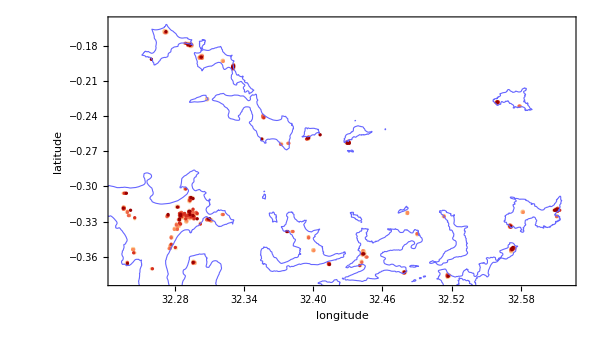

```mathematica
is=Import["~/Dropbox/Mapping/WSF2019/Uganda/dataverse_files.zip"];
polygons=Cases[is,_Polygon,Infinity];
sfac=0.00000966;
xcor=24.99;
ycor=0.014;
lo=MinMax[polygons[[All,1,All,1]]]sfac+xcor;
MinMax[polygons[[All,1,All,2]]]sfac;
LLpoly=Table[Map[{#[[1]]sfac+xcor,#[[2]]sfac+ycor}&,polygons[[i,1]]],{i,Length[polygons]}];
box1={{32.23,32.62},{-0.38,-.16}};
box={{32.,32.8},{-0.54,-.16}};
pp={};
Do[If[Min[LLpoly[[i,All,1]]]>=box[[1,1]]&&Max[LLpoly[[i,All,1]]]<=box[[1,2]] &&Min[LLpoly[[i,All,2]]]>=box[[2,1]]&&Max[LLpoly[[i,All,2]]]<=box[[2,2]],AppendTo[pp,LLpoly[[i]]]],{i,Length[LLpoly]}];
qq=Quantile[Coo[[All,3]],Range[0,1,1/7]];
posQ=Table[Flatten[Position[Coo[[All,3]],x_/;qq[[i]]<=x<qq[[i+1]]]],{i,Length[qq]-1}];
<<"~/Dropbox/Doublesex/FullDsxB/Colours";
cols=Drop[ColChoice["OrRd",Length[posQ]+1],1];
ps=0.004;
fig=Show[Table[ListPlot[Coo[[posQ[[i]],{1,2}]],PlotStyle->{PointSize[ps],cols[[i]](*GrayLevel[1-i/(Length[posQ])]*)}],{i,Length[posQ]}],(*RelSites,ContSites,*)(*ListPlot[RelVil[[All,{1,2}]],PlotStyle->Green],*)Table[Graphics[{FaceForm[None],EdgeForm[Lighter[Blue,0.4]],Polygon[pp[[i]]]}],{i,Length[pp]}],PlotRange->box1,Frame->True,FrameStyle->Black,FrameLabel->{"longitude","latitude"},ImageSize->600,AspectRatio->(box1[[2,2]]-box1[[2,1]])/(box1[[1,2]]-box1[[1,1]]),Axes->None]
```

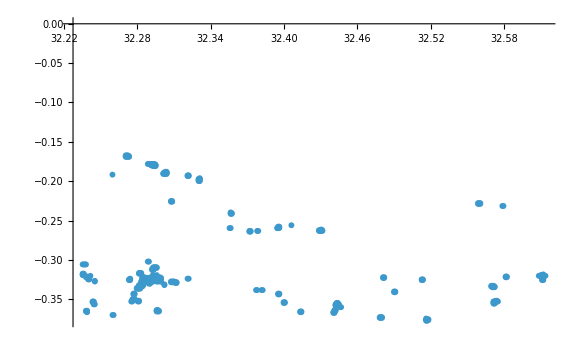

```mathematica
ListPlot[Coo[[All,{1,2}]],PlotRange->All]
```